```mathematica
res = Sum[Sum[Sum[1/k * (-1)^(k+1) *i*j, {k, 1, j}], {j, i+1, N}], {i, 1, N}]
```

∑_(i=1)^N (∑_(j=1+i)^N -i j ((-1)^j LerchPhi[-1,1,1+j]-Log[2]))

```mathematica
Sum[Sum[(Log[j] * 1) * j, {j, i+1, N}], {i, 1, N}]
```

∑_(i=1)^N (-1/12+Log[Glaisher]-Log[Hyperfactorial[i]]+Zeta^(1,0)[-1,1+N])

```mathematica
Derivative[1,0][Zeta][-1,1+N]
```

Zeta^(1,0)[-1,1+N]

```mathematica
Derivative[1,0][Zeta][s,a]
```

Zeta^(1,0)[s,a]

```mathematica
Sum[Log[Hyperfactorial[i]], {i, 1, N}]
```

∑_(i=1)^N Log[Hyperfactorial[i]]

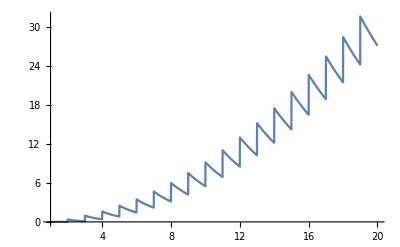

```mathematica
total[n_] := 1/n^3 * Sum[Sum[Sum[(-1)^(k+1) * i * j^2/k^2, {k, 1, j}], {j, i+1, n}], {i, 1, n}]//N
Plot[{total[l]}, {l, 1, 20}]
```

```mathematica
Sum[Sum[(Log[j] * 1) * j, {j, i+1, N}], {i, 1, N}]/.N->10//N
```

674.165

```mathematica
total[3]
```

0.972222

```mathematica
Sum[Sum[i*j, {j, i+1, N}],{i, 0, N}] //Expand
```

-N/12-N^2/8+N^3/12+N^4/8

```mathematica
taylor[ω_] := ω^2*(i^3 * j + j^3*i)
```

```mathematica
Sum[Sum[Sum[taylor[N* π* k/j], {}],{j, i+1, N}],{i, 0, N}]
```

```mathematica
D[(Sin[(a+Δ)*ω] - Sin[a*ω])/ω, ω]//FullSimplify
```

(-a ω Cos[a ω]+(a+Δ) ω Cos[(a+Δ) ω]+Sin[a ω]-Sin[(a+Δ) ω])/ω^2

```mathematica
Series[Sin[a ω]-Sin[(a+Δ) ω], {Δ, 0, 2}]
```

-ω Cos[a ω] Δ+1/2 ω^2 Sin[a ω] Δ^2+O[Δ]^3